# Compute a quasi-circular inspiral in Kerr spacetime

This notebook demonstrates how to use the KerrGeodesics package and the data in the Black Hole Perturbation Toolkit (bhptoolkit.org) to compute a quasi-circular inspiral of a small mass in to a much more massive Kerr black hole.

Load the KerrGeodeodesics package

```mathematica
<<KerrGeodesics`
```

We set the mass of the black hole to M=1 as it scales out of the problem. The spin of the black hole is denoted by ‘a’ and the mass ratio is given by ‘q’. We set q=1 here to make the plots nicer but the flux data is only calculated to linear order in the mass-ratio and the flux balance is only valid when the system is evolving adiabatically (which requires q<<1).

```mathematica
M=1;
a=0.8;
q=1;
```

Compute the constants of motion and orbital frequencies

```mathematica
{En,L,Q}={"ℰ","ℒ","𝒬"}/.KerrGeoConstantsOfMotion[a,r0,0,1];
{Ωr,Ωθ,Ωϕ}={"Ω_r","Ω_θ","Ω_ϕ"}/.KerrGeoFrequencies[a,r0,0,1];
```

Load and interpolate the flux data (change the directory to the local on your hard disk where the flux data is stored)

```mathematica
SetDirectory["~/BHPToolkit/CircularOrbitSelfForceData/Kerr/Fluxes/"];
data=Import["Flux_Edot_a"<>ToString[a]<>".dat"];
ℰdot=Interpolation[Transpose[{data[[;;,1]],q^2(data[[;;,2]]+data[[;;,3]])}]];
```

From the chain rule and flux balance (Ė=-ℰ̇) we have dr/dt=-(dE/dr)^-1 ℰ̇

```mathematica
dr0dt=-D[En,r0]^-1 ℰdot[r0]/.r0->r0[t];
```

Solve for the radial motion

```mathematica
r1=r0/.NDSolve[{r0'[t]==dr0dt,r0[0]==50},r0,{t,0,2 10^6}][[1,1]]
```

NDSolve::ndsz: At t == 127370., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

We let NDSolve run until the step size drops too small, This happens as the particle approaches the inner-most stable circular orbit (ISCO)

```mathematica
tmax=r1["Domain"][[1,2]]
```

127370.

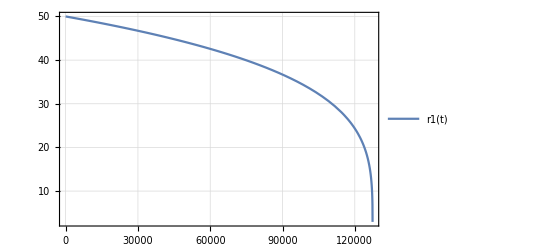

```mathematica
Plot[r1[t],{t,0,tmax},PlotTheme->"Detailed"]
```

Check that the final radius we compute is near the ISCO

```mathematica
r1[tmax]
rISCO=KerrGeoISCO[a,1]
```

2.90679

2.90664

Use the definition Ω_ϕ=dϕ/dt to solve for the azimuthal angle accumulation

```mathematica
ϕ1=ϕ/.NDSolve[{ϕ'[t]==Ωϕ/.r0->r1[t],ϕ[0]==0},ϕ,{t,0,tmax}][[1]];
```

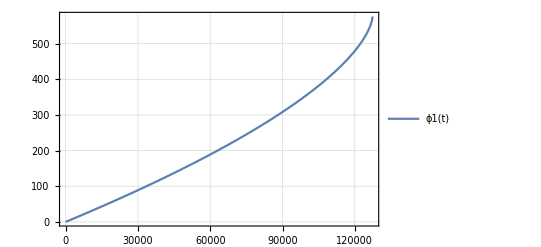

```mathematica
Plot[ϕ1[t],{t,0,tmax},PlotTheme->"Detailed"]
```

Plot the inspiral, black hole and ISCO

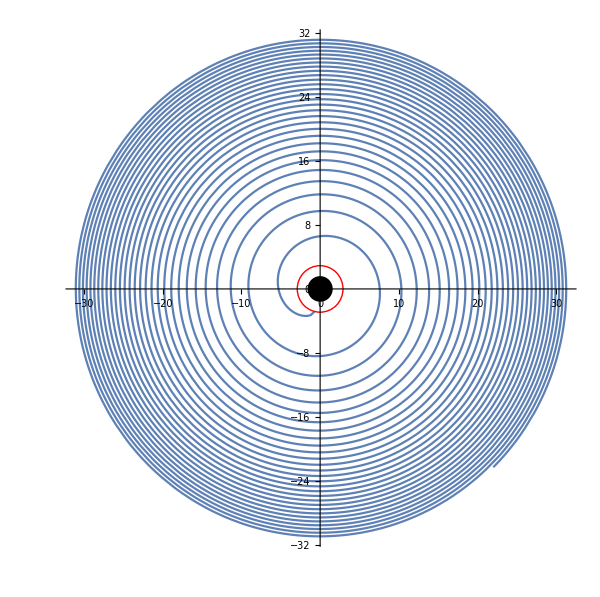

```mathematica
Show[
ParametricPlot[{r1[t]Cos[ϕ1[t]],r1[t]Sin[ϕ1[t]]},{t,tmax-2 10^4,tmax},ImageSize->600,PlotPoints->400],
Graphics[Disk[{0,0},1+Sqrt[1-a^2]]],
Graphics[{Red,Circle[{0,0},rISCO]}]
]
```